# Curvature

## Environment

```mathematica
SetDirectory[NotebookDirectory[]];
SetOptions[EvaluationNotebook[],CellContext->Notebook];
Off[NIntegrate::slwcon,NIntegrate::ncvb];
```

## Boxes

```mathematica
MakeBoxes[τ0, StandardForm] := SubscriptBox["τ", "0"]; 
MakeExpression[SubscriptBox["τ", "0"], StandardForm] := MakeExpression["τ0", StandardForm]; 
MakeBoxes[τ1, StandardForm] := SubscriptBox["τ", "1"]; 
MakeExpression[SubscriptBox["τ", "1"], StandardForm] := MakeExpression["τ1", StandardForm]; 
MakeBoxes[a3, StandardForm] := SubscriptBox["a", "3"]; 
MakeExpression[SubscriptBox["a", "3"], StandardForm] := MakeExpression["a3",StandardForm]; 
MakeBoxes[baryonDensity, StandardForm] := SubscriptBox["ρ", "b"]; 
MakeExpression[SubscriptBox["ρ", "b"], StandardForm] := MakeExpression["baryonDensity", StandardForm]; 
MakeBoxes[boltzmannConstant, StandardForm] := SubscriptBox["k", "b"]; 
MakeExpression[SubscriptBox["k", "B"], StandardForm] := MakeExpression["boltzmannConstant",StandardForm]; 
MakeBoxes[distanceFromRedshift, StandardForm] := SubscriptBox["D", "z"]; 
MakeExpression[SubscriptBox["D", "z"], StandardForm] :=MakeExpression["distanceFromRedshift", StandardForm]; 
MakeBoxes[electronDensity, StandardForm] := SubscriptBox["n", "e"]; 
MakeExpression[SubscriptBox["n", "e"], StandardForm] := MakeExpression["electronDensity",StandardForm]; 
MakeBoxes[freeElectronFraction, StandardForm] := SubscriptBox["X", "e"]; 
MakeExpression[SubscriptBox["X", "e"], StandardForm] := MakeExpression["freeElectronFraction",StandardForm]; 
MakeBoxes[heliumAbundance, StandardForm] := SubscriptBox["A", "He"]; 
MakeExpression[SubscriptBox["A", "He"], StandardForm] := MakeExpression["heliumAbundance",StandardForm]; 
MakeBoxes[heliumMass, StandardForm] := SubscriptBox["m", "He"]; 
MakeExpression[SubscriptBox["m", "He"], StandardForm] := MakeExpression["heliumMass", StandardForm]; 
MakeBoxes[hydrogenAbundance, StandardForm] := SubscriptBox["A", "H"]; 
MakeExpression[SubscriptBox["A", "H"], StandardForm] := MakeExpression["hydrogenAbundance",StandardForm]; 
MakeBoxes[hydrogenMass, StandardForm] := SubscriptBox["m", "H"]; 
MakeExpression[SubscriptBox["m", "H"], StandardForm] := MakeExpression["hydrogenMass", StandardForm]; 
MakeBoxes[kB, StandardForm] := SubscriptBox["k", "B"]; 
MakeExpression[SubscriptBox["k", "B"], StandardForm] := MakeExpression["kB",StandardForm]; 
MakeBoxes[opticalDepth, StandardForm] :=SubscriptBox["τ", "T"]; 
MakeExpression[SubscriptBox["τ", "T"], StandardForm] := MakeExpression["opticalDepth", StandardForm]; MakeBoxes[photonDensity, StandardForm] := SubscriptBox["ρ", "γ"]; 
MakeExpression[SubscriptBox["ρ", "γ"], StandardForm] := MakeExpression["photonDensity",StandardForm]; 
MakeBoxes[redshiftFromTime, StandardForm] := SubscriptBox["z", "τ"]; 
MakeExpression[SubscriptBox["z", "τ"], StandardForm] := MakeExpression["redshiftFromTime",StandardForm]; 
MakeBoxes[redshiftOfRecombination, StandardForm] := SubscriptBox["z", "*"]; 
MakeExpression[SubscriptBox["z", "*"], StandardForm] := MakeExpression["redshiftOfRecombination", StandardForm];
MakeBoxes[scaleFactorFromTime, StandardForm] := SubscriptBox["a", "τ"]; 
MakeExpression[SubscriptBox["a", "τ"], StandardForm] := MakeExpression["scaleFactorFromTime",StandardForm]; 
MakeBoxes[scatteringRate, StandardForm] := OverscriptBox["τ", "."]; 
MakeExpression[OverscriptBox["τ", "."], StandardForm] := MakeExpression["scatteringRate", StandardForm]; MakeBoxes[soundHorizon, StandardForm] := SubscriptBox["s", "*"]; 
MakeExpression[SubscriptBox["s", "*"], StandardForm] := MakeExpression["soundHorizon", StandardForm]; 
MakeBoxes[thetaPrime, StandardForm] := SuperscriptBox["θ", "′"]; 
MakeExpression[Superscript["θ", "′"], StandardForm] := MakeExpression["thetaPrime", StandardForm]; 
MakeBoxes[thomsonScatteringCrossSection, StandardForm] := SubscriptBox["σ", "T"]; 
MakeExpression[SubscriptBox["σ", "T"], StandardForm] :=MakeExpression["thomsonScatteringCrossSection", StandardForm]; 
 MakeBoxes[timeFromRedshift, StandardForm] := SubscriptBox["τ", "z"]; 
MakeExpression[SubscriptBox["τ", "z"], StandardForm] := MakeExpression["timeFromRedshift",StandardForm]; 
MakeBoxes[timeOfRecombination, StandardForm] := SubscriptBox["τ", "*"]; 
MakeExpression[SubscriptBox["τ", "*"], StandardForm] := MakeExpression["timeOfRecombination", StandardForm]; 
MakeBoxes[timePrime, StandardForm] := SuperscriptBox["τ", "′"]; 
MakeExpression[SuperscriptBox["τ", "′"], StandardForm] := MakeExpression["timePrime", StandardForm]; 
MakeBoxes[v3, StandardForm] := SubscriptBox["v", "3"]; 
MakeExpression[SubscriptBox["v", "3"], StandardForm] := MakeExpression["v3", StandardForm]; 
MakeBoxes[x0, StandardForm] := SubscriptBox["x", "0"]; 
MakeExpression[SubscriptBox["x", "0"], StandardForm] := MakeExpression["x0", StandardForm]; 
MakeBoxes[x1, StandardForm] := SubscriptBox["x", "1"]; 
MakeExpression[SubscriptBox["x", "1"], StandardForm] := MakeExpression["x1", StandardForm];
```

## Units

```mathematica
s=1;
m=1;
cm=0.01 m;
kg=1;
g=0.001 kg;
J=(kg m^2)/s^2;
K=1;
km=1000 m;
yr=60 60 24 365.25 s;
kyr=1000 yr;
Myr=1000 kyr;
Gyr=1000 Myr;
pc=3.08567758 10^13 km;
kpc=1000 pc;
Mpc=1000 kpc;
Gpc=1000 Mpc;
```

## Constants

```mathematica
G=6.67408 10^-11 m^3/(kg s^2);
ℏ=6.62607004 10^-34 J s;
Subscript[k, B]=1.380649 10^-23 J/K;
Subscript[T, 0]=2.7255 K;
θ100=1.0411;
Subscript[A, He]=0.25;
Subscript[A, H]=0.75;
Subscript[m, He]=6.6464764 10^-27 kg;
Subscript[m, H]=1.6735575 10^-27 kg;
Subscript[σ, T]=6.6524 10^-29 m^2;
Subscript[ρ, b]=2.09126×10^-26 kg m^-3;
Subscript[ρ, γ]=7.775×10^-31 kg m^-3;
```

## Clear Variables

```mathematica
ClearAll[x,Subscript[x, 0],Subscript[x, 1],Subscript[τ, 0],Subscript[τ, 1],Subscript[τ, z],Subscript[z, τ],Subscript[a, τ],Subscript[D, z],Subscript[X, e],Subscript[n, e],τ̇,Subscript[τ, T],SubStar[τ],R,SubStar[s],θ,Subscript[v, 3],Subscript[a, 3],z,x,r];
```

## Data

### Free Electron Fraction

This file is the output of the Recfast++ program .  It' s a collection of redshifts and the expected free election fraction at that time based on a cosmological model.

```mathematica
freeElectronFractionData=Import["C:\\Users\\DonaldAirey\\source\\repos\\recfast-cplusplus\\Recfast\\output\\Xe_Recfast.dat","Table"];
```

## Functions

### Distance from Proper Time

```mathematica
x=Subscript[v, 3] τ-1/2 Subscript[a, 3] τ^2;
Subscript[x, 0]=x/.{τ->Subscript[τ, 0]};
Subscript[x, 1]=x/.{τ->Subscript[τ, 1]};
```

### Proper Time from Redshift

```mathematica
Subscript[τ, z][z_]=Subscript[τ, 0]/.Simplify[Solve[z==(Subscript[x, 1]-Subscript[x, 0])/Subscript[x, 0],Subscript[τ, 0]]]⟦1⟧
```

(v_3+v_3 z-√((1+z) (v_3^2+v_3^2 z-2 a_3 v_3 τ_1+a_3^2 τ_1^2)))/(a_3+a_3 z)

### Redshift from Proper Time

```mathematica
Subscript[z, τ][τ_]=z/.Simplify[Solve[z==(Subscript[x, 1]-Subscript[x, 0])/Subscript[x, 0],z]/.{Subscript[τ, 0]->τ}][[1]]
```

-((τ-τ_1) (-2 v_3+a_3 (τ+τ_1)))/(τ (-2 v_3+a_3 τ))

### Scale Factor from Proper Time

```mathematica
Subscript[a, τ][τ_]=Simplify[1/(1+Subscript[z, τ][τ])]
```

(τ (-2 v_3+a_3 τ))/(τ_1 (-2 v_3+a_3 τ_1))

### Distance from Redshift

```mathematica
Subscript[D, z][z_]=(z Subscript[τ, 1] (2 Subscript[v, 3]-Subscript[a, 3] Subscript[τ, 1]))/(2+z);
```

### Electron Number Density

```mathematica
Subscript[X, e]=Interpolation[freeElectronFractionData⟦All,{1,2}⟧];
```

```mathematica
Subscript[n, e][τ_]=Subscript[X, e][Subscript[z, τ][τ]] Subscript[ρ, b]/(Subscript[A, H] Subscript[m, H]+Subscript[A, He] Subscript[m, He])(1+Subscript[z, τ][τ])^3;
```

### Thomson Scattering Rate from Proper Time

Note that the electron number density, n_e is in units of cm^-3. Thompson cross section, σ_T, is in units of cm^2. The scale factor, a, is unit-less.  Note that we convert the value to units of s^-1 by multiplying by the speed of light.  This is because the Optical Depth integrates over time.  When we multiply inverse time by time,  τ, we get a unit-less value which are the units of Optical Depth.  All of the textbooks seem to leave this important step out.  It’s critical that the units give us the right answer.

```mathematica
τ̇[τ_]:=Subscript[n, e][τ] Subscript[σ, T] Subscript[a, τ][τ] (Subscript[v, 3]-Subscript[a, 3] τ)
```

### Optical Depth for Thomson Scattering from Proper Time

```mathematica
Subscript[τ, T][τ_]:=∫_τ^Subscript[τ, 1] τ̇[τ']ⅆ τ'
```

### Time of Recombination

```mathematica
SubStar[τ]:=τ/.FindRoot[Subscript[τ, T][τ]==1,{τ,Subscript[τ, z][1200]}];
```

### Baryon-Photon Momentum Density Ratio

```mathematica
R[τ_]=3/4(Subscript[ρ, b](1+Subscript[z, τ][τ])^3)/(Subscript[ρ, γ](1+Subscript[z, τ][τ])^4);
```

### Sound Horizon

Note that the sound horizon is twice the distance that sound travels in time, τ . The diameter (which is the angle that is measured in the CMB) is twice the distance of the radius .

```mathematica
SubStar[s][τ_]:=∫_0^τ ((Subscript[v, 3]-Subscript[a, 3] τ')+(Subscript[v, 3]-Subscript[a, 3] τ')/(√(3 (1+R[τ']))))ⅆ τ';
```

### Angle from Curvature, Distance and Sound Horizon

```mathematica
θ[k_,r_,SubStar[s]:_]=θ/.Solve[SubStar[s]==∫_0^θ Sin[r √k]/(√k)ⅆ θ',θ]⟦1⟧;
```

## QES Constants

```mathematica
Subscript[v, 3]=3.17840613545762×10^8;
Subscript[a, 3]=3.64661613355436×10^-11;
Subscript[τ, 1]=4.94928856911811×10^17;
```

## Optical Depth

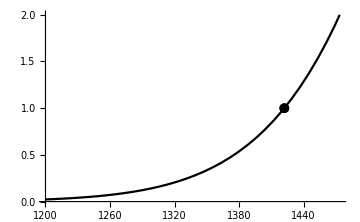

```mathematica
opticalDepthPlot=Plot[Subscript[τ, T][Subscript[τ, z][z]],{z,1600,1200},PlotStyle->{Black},PlotRange->{{1600,1200},{0,2}}];
opticalDepthMarkerPlot=ListPlot[{{Subscript[z, τ][SubStar[τ]],1.}},PlotStyle->{Black},PlotMarkers->{Automatic,Medium}];
Show[{opticalDepthPlot,opticalDepthMarkerPlot},ImageSize->Medium]
```

## Red Shift of CMB and Radius of Curvature

The optimization above is inconclusive because, as we approach a perfect flatness, there isn’t enough information in the signal. So we skip ahead and calculate the angular scale for a flat topology.

```mathematica
z=Subscript[z, τ][SubStar[τ]]
x=Subscript[v, 3] Subscript[τ, 1]-1/2 Subscript[a, 3] Subscript[τ, 1]^2
r=r/.FindInstance[{θ[1/r^2,Subscript[D, z][z],SubStar[s][Subscript[τ, z][z]]] 100==θ100&&r>10^26},{r}]⟦1⟧
CopyToClipboard[ExportString[{z,SubStar[s][Subscript[τ, z][z]],r},"TSV"]];
```

1422.

1.52842×10^26

1.01235×10^26